```mathematica
(*To Do
- Animate
- Create a recovery period
- Establish incubation period
```

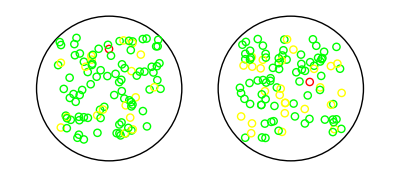

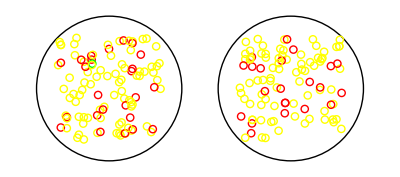

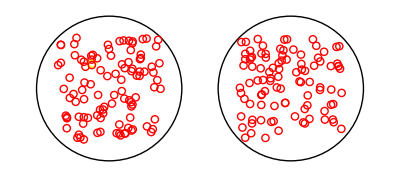

```mathematica
Transfer =10;
Infectious =1;
Days=3;
InfectedA=1;
InfectedB=1;
PopA =Table[{k*A,RandomReal[{-Sqrt[2],Sqrt[2]}],RandomReal[{-Sqrt[2],Sqrt[2]}],"u"},{k,1,100}];
PopB = Table[{k*B,RandomReal[{5-Sqrt[2],5+Sqrt[2]}],RandomReal[{-Sqrt[2],Sqrt[2]}],"u"},{k,1,100}];
For[j=1,j<InfectedA+1,j++,
PopA[[j]][[4]]="i"];
For[j=1,j<InfectedB+1,j++,
PopB[[j]][[4]]="i"];

For[k=0,k<Days,k++,

PopA=Replace[PopA,"n"->"i",2];
PopB=Replace[PopB,"n"->"i",2];

TotalPeopleA = Length[PopA];
PeopleMetA = Random[Integer,{10,20}];
(*Print["People Met in City A"PeopleMetA];*)

TotalPeopleB = Length[PopB];
PeopleMetB = Random[Integer,{10,20}];
(*Print["People Met in City B"PeopleMetB];*)


For[j=1,j<TotalPeopleA+1, j++,
For[i=0,i<PeopleMetA,i++,
ContactA =Random[Integer,{1,TotalPeopleA}];
If[PopA[[ContactA]][[4]]=="i",
If[PopA[[j]][[4]]≠"i",
If[PopA[[j]][[4]]≠"n",
If[Random[Integer,{1,10}]> Infectious,
PopA[[j]][[4]]="n"]
]
],
If[PopA[[ContactA]][[4]]≠"n",
If[PopA[[j]][[4]]=="i",
If[Random[Integer,{1,10}]> Infectious,
PopA[[ContactA]][[4]]="n"]
]
]
]
]
]

For[j=1,j<TotalPeopleB+1, j++,
For[i=0,i<PeopleMetB,i++,
ContactB =Random[Integer,{1,TotalPeopleB}];
If[PopB[[ContactB]][[4]]=="i",
If[PopB[[j]][[4]]≠"i",
If[PopB[[j]][[4]]≠"n",
If[Random[Integer,{1,10}]> Infectious,
PopB[[j]][[4]]="n"]
]
],
If[PopB[[ContactB]][[4]]≠"n",
If[PopB[[j]][[4]]=="i",
If[Random[Integer,{1,10}]> Infectious,
PopB[[ContactB]][[4]]="n"]
]
]
]
]
];

ToA=RandomChoice[PopB,Transfer];
ToB=RandomChoice[PopA,Transfer];
PopA=Complement[PopA,ToB];
PopB=Complement[PopB,ToA];
For[i=1,i<Length[ToA]+1,i++,
ToA[[i]][[2]]=ToA[[i]][[2]]-5
];
For[i=1,i<Length[ToB]+1,i++,
ToB[[i]][[2]]=ToB[[i]][[2]]+5
];
PopA=Join[PopA,ToA];
PopB=Join[PopB,ToB];

Print[
Graphics[
Join[
{{Circle[{0,0},2]},{Circle[{5,0},2]}},
Table[{
If[
PopA[[i]][[4]]=="u",
Green,
If[
PopA[[i]][[4]]=="i",
Red,Yellow]
],
Circle[{PopA[[i]][[2]],PopA[[i]][[3]]},.1]},{i,1,Length[PopA]}
],
Table[{
If[
PopB[[i]][[4]]=="u",
Green,
If[
PopB[[i]][[4]]=="i",
Red,Yellow]
],
Circle[{PopB[[i]][[2]],PopB[[i]][[3]]},.1]},{i,1,Length[PopB]}
]
]
]];
]
```